```mathematica
SetDirectory[NotebookDirectory[]];
```

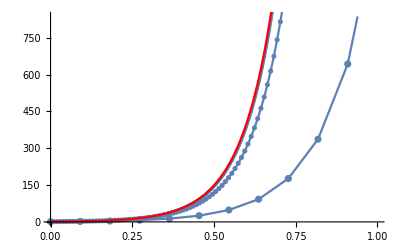

```mathematica
n11 = Import["./outputs/uloha1/a_11n.csv","CSV"];
n101 = Import["./outputs/uloha1/a_101n.csv","CSV"];
n1001 = Import["./outputs/uloha1/a_1001n.csv","CSV"];
DSolve[{x'[t]==10 x[t], x[0]==1},x,t];
Show[
ListPlot[n11],
ListLinePlot[n11],
ListPlot[n101],
ListLinePlot[n101],
ListPlot[n1001],
ListLinePlot[n1001],
Plot[Evaluate[x[t]/.%],{t,0,1}, PlotStyle->Red]
]
```

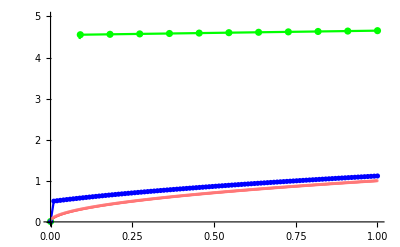

```mathematica
n11 = Import["./outputs/uloha1/b_11n.csv","CSV"];
n101 = Import["./outputs/uloha1/b_101n.csv","CSV"];
n1001 = Import["./outputs/uloha1/b_1001n.csv","CSV"];
DSolve[{x'[t]==1/(2 x[t]), x[0.0001]==0.01},x,t];
Show[
Plot[Evaluate[x[t]/.%],{t,0,1}, PlotStyle->Red, PlotRange->{0,5}],
ListPlot[n11, PlotStyle->Green],
ListLinePlot[n11, PlotStyle->Green],
ListPlot[n101, PlotStyle->Blue],
ListLinePlot[n101, PlotStyle->Blue],
ListPlot[n1001, PlotStyle->{Pink, Opacity[0.3]}](*,
ListLinePlot[n1001, PlotStyle->Pink]*)
]
```

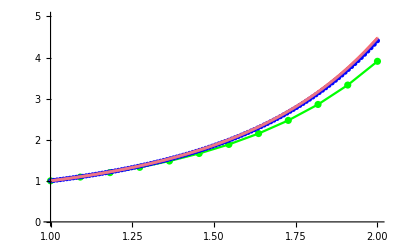

```mathematica
n11 = Import["./outputs/uloha1/c_11n.csv","CSV"];
n101 = Import["./outputs/uloha1/c_101n.csv","CSV"];
n1001 = Import["./outputs/uloha1/c_1001n.csv","CSV"];
DSolve[{x'[t]==t x[t], x[1]==1},x,t];
Show[
Plot[Evaluate[x[t]/.%],{t,1,2}, PlotStyle->Red, PlotRange->{0,5}],
ListPlot[n11, PlotStyle->Green],
ListLinePlot[n11, PlotStyle->Green],
ListPlot[n101, PlotStyle->Blue],
ListLinePlot[n101, PlotStyle->Blue],
ListPlot[n1001, PlotStyle->{Pink, Opacity[0.3]}](*,
ListLinePlot[n1001, PlotStyle->Pink]*)
]
```

Uloha 2

```mathematica
DSolve[{x'[t]==10 x[t], x[0]==1},x,t];
Evaluate[x[t]/.%]/.t->1//N
```

{22026.5}